```mathematica
F[x_,y_,z_]:={
Cos[z]-Sin[y],
x+ Cos[y],
x+y
}
Manipulate[
Module[{v},
v=Curl[F[x,y,z],{x,y,z}]/.x->x0/.y->y0/.z->z0;
Show[
StreamPlot3D[F[x,y,z],{x,-2,2},{y,-2,2},{z,-2,2}],
Graphics3D[{Black,Arrowheads[0.1],Arrow[Tube[{x0,y0,z0}+#&/@{{0,0,0},v},0.1]]}]
]
],
{x0,-1,1},
{y0,-1,1},
{z0,-1,1}
]
```

-Graphics3D-

{0,0,Cos[y]}

```mathematica
Curl[{
y,
Cos[z],
2
},{x,y,z}]
```

{Sin[z],0,-1}

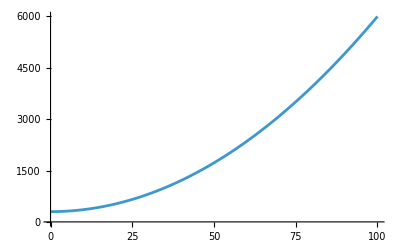

```mathematica
Module[{R=100},
Plot[5700(d/R)^2+300, {d,0,R}]
]
```

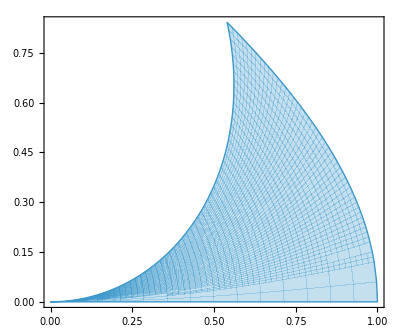

-Graphics-

```mathematica
ParametricPlot[{u Cos[v],v Sin[u]},{u,0,1},{v,0,u}]
```

```mathematica
NIntegrate[
Abs[Det[D[{u Cos[v],v Sin[u]},{{u,v}}]]],
{u,0,1},{v,0,u}
]
```

0.314082

```mathematica
Module[{r=1/2,R=1,sp1=20,sp2=400},
ParametricPlot3D[
{R Cos[θ],R Sin[θ],0} + r{Cos[θ]Sin[20θ],Sin[θ]Sin[20θ],Cos[20θ]}+
0.1 Cos[400θ]{(-2 R Cos[θ]+361 Sin[19 θ]+441 Sin[21 θ])/(√(644802+4 R^2+1598 Cos[40 θ]-3208 R Sin[20 θ])),(361 Cos[19 θ]-441 Cos[21 θ]-2 R Sin[θ])/(√(644802+4 R^2+1598 Cos[40 θ]-3208 R Sin[20 θ])),-(400 Cos[20 θ])/(√(322401/2+R^2+799/2 Cos[40 θ]-802 R Sin[20 θ]))} +
0.1 Sin[400θ]{-((10 √2 (42 R Cos[19 θ]+38 R Cos[21 θ]-1602 Sin[θ]+19 Sin[39 θ]+21 Sin[41 θ]))/(√(516485203+8 R^2 (162203+R^2)+(635196-4824 R^2) Cos[40 θ]-399 Cos[80 θ]+16 R (-321601-402 R^2+Cos[40 θ]) Sin[20 θ]))),(10 √2 (-1602 Cos[θ]-19 Cos[39 θ]+21 Cos[41 θ]+42 R Sin[19 θ]-38 R Sin[21 θ]))/(√(516485203+8 R^2 (162203+R^2)+(635196-4824 R^2) Cos[40 θ]-399 Cos[80 θ]+16 R (-321601-402 R^2+Cos[40 θ]) Sin[20 θ])),(√2 (1201+2 R^2+399 Cos[40 θ]-804 R Sin[20 θ]))/(√(516485203+8 R^2 (162203+R^2)+(635196-4824 R^2) Cos[40 θ]-399 Cos[80 θ]+16 R (-321601-402 R^2+Cos[40 θ]) Sin[20 θ]))}
,
{θ,0,0.2π}
(*,{ϕ,0,2π}*)
]
]
```

-Graphics3D-

```mathematica
s0[θ_]:={R Cos[θ],R Sin[θ],0};
s1[θ_]:={R Cos[θ],R Sin[θ],0} + Sin[20θ]{-Cos[θ],-Sin[θ],0} + Cos[20θ]{0,0,1}
FullSimplify[Normalize[D[s1[θ],{θ,2}]],R>0&&θ∈Reals]
FullSimplify[
Normalize[Cross[
D[s1[θ],{θ,1}],
D[s1[θ],{θ,2}]
]
],
R>0&&θ∈Reals]
```

{(-2 R Cos[θ]+361 Sin[19 θ]+441 Sin[21 θ])/(√(644802+4 R^2+1598 Cos[40 θ]-3208 R Sin[20 θ])),(361 Cos[19 θ]-441 Cos[21 θ]-2 R Sin[θ])/(√(644802+4 R^2+1598 Cos[40 θ]-3208 R Sin[20 θ])),-(400 Cos[20 θ])/(√(322401/2+R^2+799/2 Cos[40 θ]-802 R Sin[20 θ]))}

```mathematica
{-((10 √2 (42 R Cos[19 θ]+38 R Cos[21 θ]-1602 Sin[θ]+19 Sin[39 θ]+21 Sin[41 θ]))/(√(516485203+8 R^2 (162203+R^2)+(635196-4824 R^2) Cos[40 θ]-399 Cos[80 θ]+16 R (-321601-402 R^2+Cos[40 θ]) Sin[20 θ]))),(10 √2 (-1602 Cos[θ]-19 Cos[39 θ]+21 Cos[41 θ]+42 R Sin[19 θ]-38 R Sin[21 θ]))/(√(516485203+8 R^2 (162203+R^2)+(635196-4824 R^2) Cos[40 θ]-399 Cos[80 θ]+16 R (-321601-402 R^2+Cos[40 θ]) Sin[20 θ])),(√2 (1201+2 R^2+399 Cos[40 θ]-804 R Sin[20 θ]))/(√(516485203+8 R^2 (162203+R^2)+(635196-4824 R^2) Cos[40 θ]-399 Cos[80 θ]+16 R (-321601-402 R^2+Cos[40 θ]) Sin[20 θ]))}//N
```

{-((14.1421 (42. R Cos[19. θ]+38. R Cos[21. θ]-1602. Sin[θ]+19. Sin[39. θ]+21. Sin[41. θ]))/(√(5.16485×10^8+8. R^2 (162203.+R^2)+(635196.-4824. R^2) Cos[40. θ]-399. Cos[80. θ]+16. R (-321601.-402. R^2+Cos[40. θ]) Sin[20. θ]))),(14.1421 (-1602. Cos[θ]-19. Cos[39. θ]+21. Cos[41. θ]+42. R Sin[19. θ]-38. R Sin[21. θ]))/(√(5.16485×10^8+8. R^2 (162203.+R^2)+(635196.-4824. R^2) Cos[40. θ]-399. Cos[80. θ]+16. R (-321601.-402. R^2+Cos[40. θ]) Sin[20. θ])),(1.41421 (1201.+2. R^2+399. Cos[40. θ]-804. R Sin[20. θ]))/(√(5.16485×10^8+8. R^2 (162203.+R^2)+(635196.-4824. R^2) Cos[40. θ]-399. Cos[80. θ]+16. R (-321601.-402. R^2+Cos[40. θ]) Sin[20. θ]))}